```mathematica
fMain="divBRefinedVcat";
```

```mathematica
fMod="BSurfaceTest";
fMod="";
```

```mathematica
mSz=10;
divLst={80,16,16};
itNum=1000;
seed=1000;
nDim=3;
```

```mathematica
nRes=3;
```

```mathematica
{attrDimLst,valDimLst,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim,"attrMoreLst"->{"nRes"},"valMoreLst"->{3}];
```

```mathematica
fNeighborVcatMain="divBErrNeighborsVcat";
```

```mathematica
fName=fNameFun[fMain,attrDimLst,valDimLst,fMod,jld2Type];
```

```mathematica
fNeighborVcatName=fNameFun[fNeighborVcatMain,attrDimLst,valDimLst,fMod,jld2Type];
```

```mathematica
divBNeighborAbsSumVcat=readJuliaVar[fNeighborVcatName,"divBErrNeighborAbsSumVcat"];
```

```mathematica
divBNeighborAbsSumVcat⟦1⟧//Dimensions
```

{1,172499,1}

```mathematica
Hlst=HistogramList[divBNeighborAbsSumVcat⟦1⟧//Flatten];
```

```mathematica
Hlst
```

{{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5,29/10,3,31/10,16/5,33/10,17/5,7/2,18/5,37/10,19/5,39/10,4,41/10},{38196,0,0,0,0,0,0,0,0,0,126757,0,0,0,0,0,0,0,0,0,7214,0,0,0,0,0,0,0,0,0,310,0,0,0,0,0,0,0,0,0,22}}

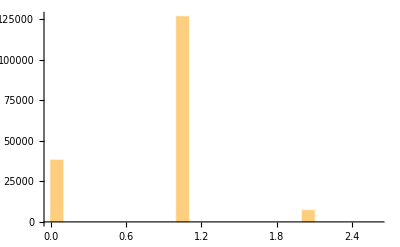

```mathematica
Histogram[divBNeighborAbsSumVcat⟦1⟧//Flatten]
```

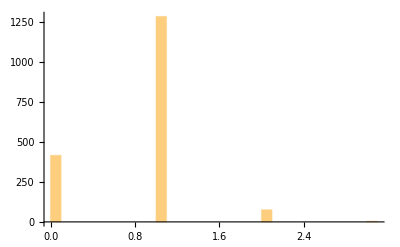

```mathematica
Histogram[divBNeighborAbsSumVcat⟦1⟧//Flatten]
```

```mathematica
4402-416
```

3986

```mathematica
fName
```

divBRefinedVcat_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_10_seed_1000_nRes_3_BSurfaceTest.jld2

```mathematica
Dimensions[divBLstVcat2]
```

{2,1,4402,3}

```mathematica
divBLstVcat2=readJuliaVar[fName,"divBLstVcat"];
```

```mathematica
BMaxLstVcat=readJuliaVar[fName,"BMaxLstVcat"];
```

```mathematica
BDiffLstVcat=readJuliaVar[fName,"BDiffLstVcat"];
```

```mathematica
BMaxDiffLstErrCat=readJuliaVar[fName,"BMaxDiffLstErrCat"];
```

```mathematica
BRemainDiffLstErrVcat=readJuliaVar[fName,"BRemainDiffLstErrVcat"];
```

```mathematica
Dimensions[BRemainDiffLstErrVcat⟦1,1⟧]
```

{8900,1}

```mathematica
Min[BRemainDiffLstErrVcat⟦1,1⟧]
```

-3.14382

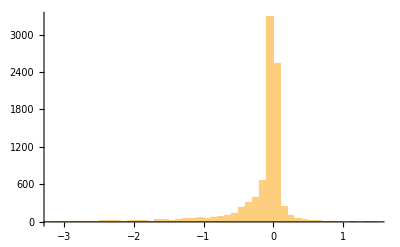

```mathematica
Histogram[BRemainDiffLstErrVcat⟦1,1⟧//Flatten,PlotRange->All]
```

```mathematica
BMaxDiffLstErrCat⟦1,1⟧//Dimensions
```

{1780,1}

```mathematica
Max[BMaxDiffLstErrCat⟦1,1⟧]
```

-1.28724

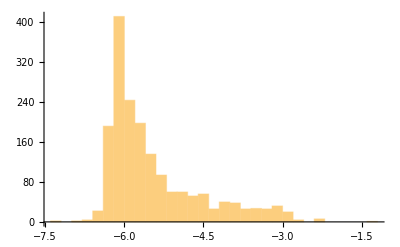

```mathematica
Histogram[BMaxDiffLstErrCat⟦1,1⟧//Flatten]
```

```mathematica
Max[BDiffLstVcat⟦1,1,All,1⟧]
```

3.97538

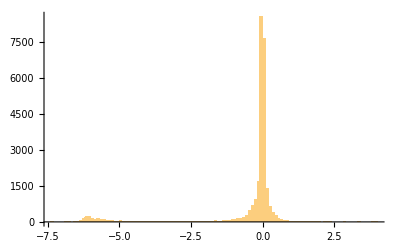

```mathematica
Histogram[BDiffLstVcat⟦1,1,All,1⟧,PlotRange->All]
```

```mathematica
Histogram[Bdiff]
```

```mathematica
BMaxLstErrVcat⟦2,1⟧//Dimensions
```

{4388,3}

```mathematica
BMaxLstNonErrVcat=readJuliaVar[fName,"BMaxLstNonErrVcat"];
```

```mathematica
BMaxLstErrVcat=readJuliaVar[fName,"BMaxLstErrVcat"];
```

```mathematica
BRemainLstVcat=readJuliaVar[fName,"BRemainLstVcat"];
```

```mathematica
BRemainLstErrVcat=readJuliaVar[fName,"BRemainLstErrVcat"];
```

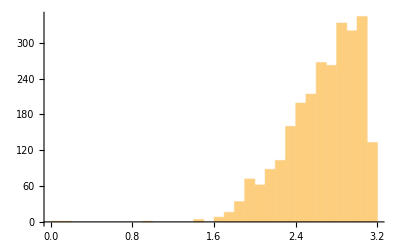

```mathematica
Histogram[BMaxLstNonErrVcat⟦1,1,All,1⟧]
```

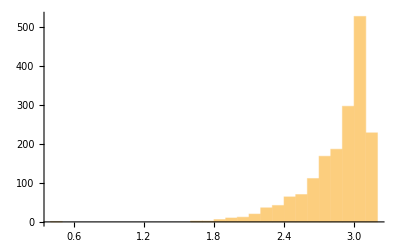

```mathematica
Histogram[BMaxLstErrVcat⟦1,1,All,1⟧]
```

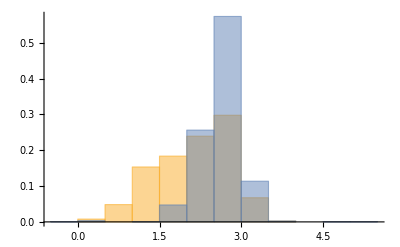

```mathematica
Histogram[{BMaxLstErrVcat⟦1,1,All,2⟧,BMaxLstNonErrVcat⟦1,1,All,2⟧},Automatic,"Probability"]
```

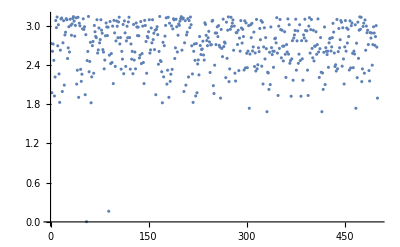

```mathematica
ListPlot[BMaxLstNonErrVcat⟦1,1,1;;500,1⟧]
```

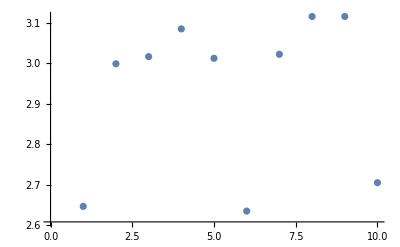

```mathematica
ListPlot[BMaxLstErrVcat⟦1,1,1;;10,1⟧]
```

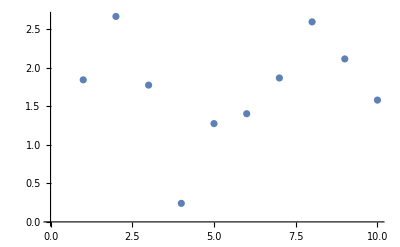

```mathematica
ListPlot[BMaxLstErrVcat⟦1,1,1;;10,3⟧]
```

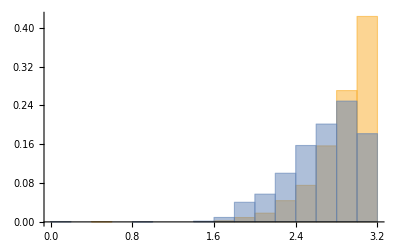

```mathematica
Histogram[{BMaxLstErrVcat⟦1,1,All,1⟧,BMaxLstNonErrVcat⟦1,1,All,1⟧},Automatic,"Probability"]
```

```mathematica
BMaxLstVcat//Dimensions
```

{2,1,4402,3}

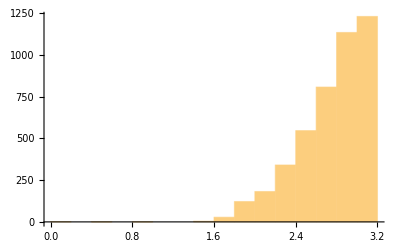

```mathematica
Histogram[BMaxLstVcat⟦1,1,All,1⟧]
```

```mathematica
Histogram[BRemainErrLstVcat⟦1,1,All,1⟧]
```

Part::partd: Part specification BRemainErrLstVcat⟦1,1,All,1⟧ is longer than depth of object.

Histogram::ldata: BRemainErrLstVcat⟦1,1,All,1⟧ is not a valid dataset or list of datasets.

Histogram[BRemainErrLstVcat⟦1,1,All,1⟧]

```mathematica
Min[BRemainLstErrVcat⟦1,1,All,1⟧]
```

-2.01341

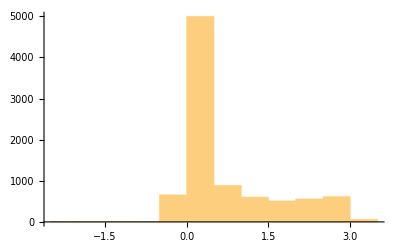

```mathematica
Histogram[BRemainLstErrVcat⟦1,1,All,1⟧]
```

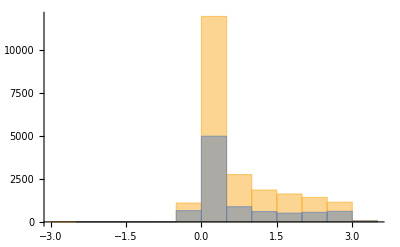

```mathematica
Histogram[{BRemainLstVcat⟦1,1,All,1⟧,BRemainLstErrVcat⟦1,1,All,1⟧}]
```

```mathematica
BRemainLstVcat⟦1,1,1;;10,2⟧
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
BRemainLstVcat//Dimensions
```

{2,1,22010,3}

```mathematica
BMaxLstVcat//Dimensions
```

{2,1,4402,3}

```mathematica
ArrayReshape
```

```mathematica
Dimensions[divBLstVcat⟦1⟧]
```

{}

```mathematica
divBLstVcat⟦1⟧//Dimensions
```

{1,4402,3}

```mathematica
divBLstVcatSq=rmSingletonDims/@divBLstVcat;
```

```mathematica
divBLstVcatSq⟦1,1;;10,3⟧
```

{1.,0.,-7.0679×10^-17,3.53395×10^-17,1.,1.,-4.96962×10^-18,1.,1.,1.}

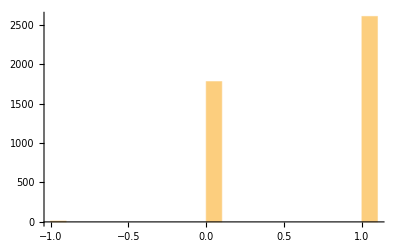

```mathematica
Histogram[divBLstVcatSq⟦1,All,3⟧]
```

```mathematica
divBLstVcat2//Dimensions
```

{2,1,4402,3}

```mathematica
divBLstVcat⟦1,1,1;;10,3⟧
```

{1.,0.,-7.0679×10^-17,3.53395×10^-17,1.,1.,-4.96962×10^-18,1.,1.,1.}

```mathematica
Histogram[divBLstVcat⟦1,1,All,3⟧]
```

-Graphics-

```mathematica
divBLstVcat2⟦1,1,1;;10,1⟧
```

{-2.73122×10^-16,3.04389×10^-17,1.,-5.01103×10^-17,1.45706×10^-16,-2.10915×10^-16,1.54265×10^-16,-8.9039×10^-18,-6.18786×10^-16,9.5251×10^-17}

```mathematica
Histogram[divBLstVcat2⟦1,1,All,3⟧]
```

-Graphics-

```mathematica
hLst=HistogramList[divBLstVcatSq⟦1,All,3⟧];
```

```mathematica
hLst
```

{{-1,-9/10,-4/5,-7/10,-3/5,-1/2,-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10},{11,0,0,0,0,0,0,0,0,0,1780,0,0,0,0,0,0,0,0,0,2606}}

```mathematica
Directory[]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules